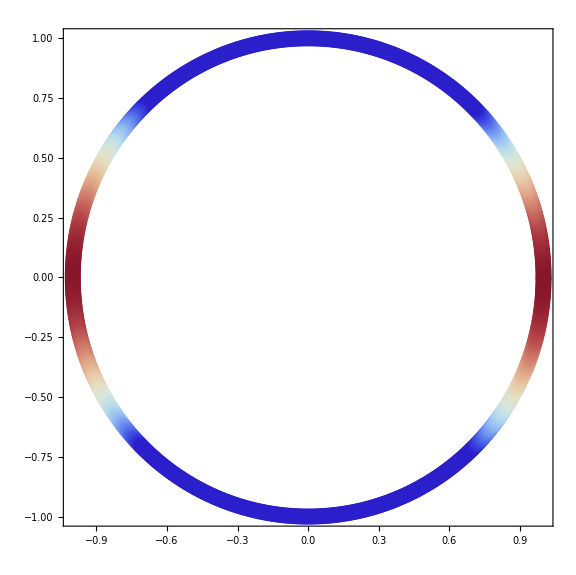

Max ω = 3

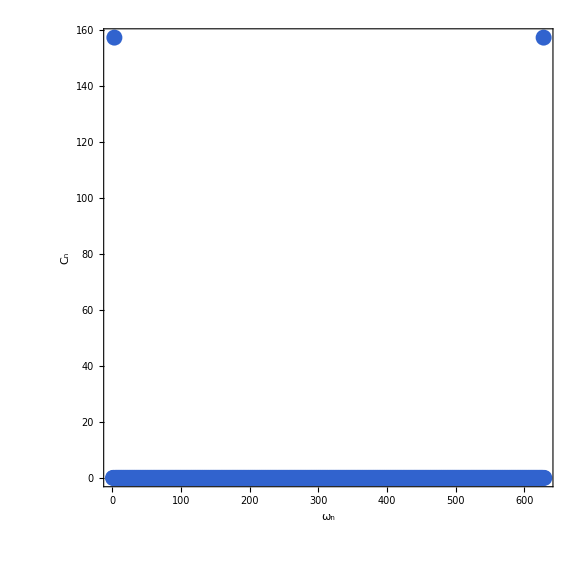

```mathematica
dk=0.01;
colordata=Table[Cos[2x],{x,0,2Pi,dk}];
fs=Table[{Cos[x],Sin[x]},{x,0,2Pi,dk}];
plotGap[fs_,colordata_]:=Module[{colorFunction,color},colorFunction[x_]:=ColorData["ThermometerColors"][x];
Graphics[Table[{colorFunction[colordata[[i]]],PointSize[0.02],Point[fs[[i]]]},{i,1,Length[fs]}],
Frame->True,ImageSize->Large,FrameTicksStyle->Directive[Black,24,FontFamily->"Times New Roman"],
FrameStyle->Directive[Black,FontFamily->"Times New Roman"]]]
plotGap[fs,colordata]
fourierCoff[da_]:=Module[{maxω,da1},da1=Abs[Fourier[da]]^2;maxω=Ordering[da1][[Length[da1]-1]];
Print[Style[StringJoin["Max ω = ",ToString[maxω]],24,Blue,FontFamily->"Times New Roman"]];da1]
coff=fourierCoff[colordata];
ListPlot[coff,PlotRange->All,PlotStyle->Directive[PointSize[0.02]],AspectRatio->1,
FrameLabel->{Style["ω_n",24,FontFamily->"Times New Roman"],Style["C_n",24,FontFamily->"Times New Roman"]}]
```